## Code

```mathematica
repository = ParentDirectory[NotebookDirectory[]];
PacletDirectoryLoad[FileNameJoin[{repository,"Recursor"}]];
Needs["WolframInstitute`Recursor`"];
Needs["Wolfram`Lambda`"];

data = Import[FileNameJoin[{repository, "docs", "notes", "data", "OEISCorpusV2.json.gz"}], {"GZIP", "RawJSON"}];
{p8, p20} = Lookup[data["Protocols"], {"P8", "P20"}];
v1 = data["V1"];
records = Association[
	(#Key -> Join[#1, Association[
		"Terms" -> FromDigits /@ #Terms,
		"Program" -> ParseRecursor[#Program]]
	]&) /@ Join[data["Examples"], data["Failures"]]
];
program[id_] := records[id]["Program"];
share[count_] := N[(100 count)/data["Eligible"]];
cumulative[protocol_, key_] := Accumulate[Lookup[protocol["Rounds"], key]];
passing[protocol_] := Association[(#Method -> (100. #TestFits)/Max[1,#TrainingFits]&) /@ protocol["Methods"]];
computed[id_, amount_] := Table[
	EvaluateRecursor[program[id], n, "MaxSteps" -> 5000000, "TimeLimit"->20],
	{n, records[id]["Offset"], records[id]["Offset"] + amount - 1}
] /. _Failure -> Missing[];

predictionPlot[id_, count_ : All] := Module[{record = records[id], amount, inputs, observed},
	amount = If[count === All, Length[record["Terms"]], Min[count, Length[record["Terms"]]]];
	inputs = Range[record["Offset"], record["Offset"] + amount - 1];
	observed = Take[record["Terms"], amount];
	If[Max[observed] > 200 Max[1, Median[observed]], ListLogPlot, ListPlot][
		{Transpose[{inputs, observed}],Transpose[{inputs, computed[id, amount]}]},
		Joined -> {True, False},
		PlotMarkers -> {{"●", 7}, {"□", 13}},
		PlotLegends -> {"OEIS", "Recursor"},
		Frame -> True,
		FrameLabel -> {"Index n", "a(n)"},
		PlotLabel -> record["ID"],
		GridLines -> {{record["Offset"] + record["TrainingTerms"] - 0.5}, None},
		PlotRange -> All
	]
]
```

## Init

```mathematica
metrics=Association[
"Eligible"->data["Eligible"],
"V1Predicted"->v1["PrimaryFits"],
"V2Predicted"->p8["TestFits"],
"Gain"->N[p8["TestFits"]/v1["PrimaryFits"]],
"V2PredictedPercent"->share[p8["TestFits"]],
"V2PredictedEveryTerm"->p8["AllRecordedFits"],
"Represented"->p20["TrainingFits"],
"RepresentedPercent"->share[p20["TrainingFits"]],
"RepresentedEveryLaterTerm"->p20["AllRecordedFits"]
];
```

## Results

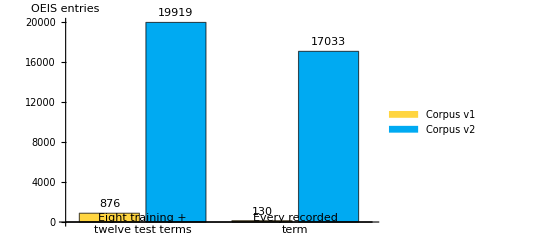

```mathematica
BarChart[{{v1["PrimaryFits"],p8["TestFits"]},{v1["AllRecordedFits"],p8["AllRecordedFits"]}},ChartLabels->{{"Eight training +\ntwelve test terms","Every recorded\nterm"},None},ChartLegends->{"Corpus v1","Corpus v2"},LabelingFunction->Above,AxesLabel->{None,"OEIS entries"}]
```

Figure 1. From eight terms, Recursor now predicts the next twelve for 19,919 sequences. Corpus v1 predicted 876.

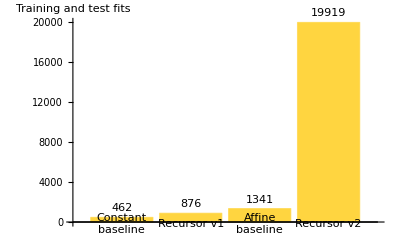

```mathematica
BarChart[{v1["ConstantBaseline"],v1["PrimaryFits"],v1["AffineBaseline"],p8["TestFits"]},ChartLabels->{"Constant\nbaseline","Recursor v1","Affine\nbaseline","Recursor v2"},LabelingFunction->Above,AxesLabel->{None,"Training and test fits"}]
```

Figure 2. Corpus v1 stayed below a straight-line baseline of 1,341. Corpus v2 is 14.9 times above it.

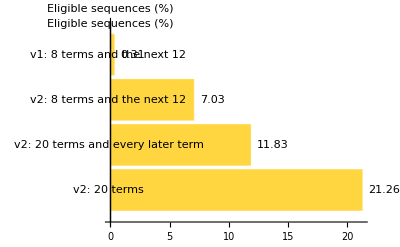

```mathematica
BarChart[Round[share/@{p20["TrainingFits"],p20["AllRecordedFits"],p8["TestFits"],v1["PrimaryFits"]},0.01],BarOrigin->Left,ChartLabels->{"v2: 20 terms","v2: 20 terms and every later term","v2: 8 terms and the next 12","v1: 8 terms and the next 12"},LabelingFunction->After,AxesLabel->{"Eligible sequences (%)",None}]
```

Figure 3. Share of the 283,167 eligible sequences. From twenty terms, 60,199 sequences have a program.

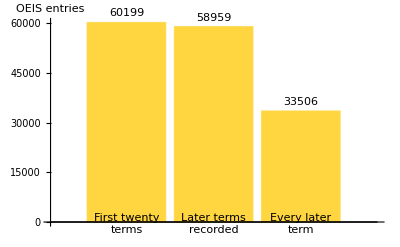

```mathematica
BarChart[Lookup[p20,{"TrainingFits","WithLaterTerms","AllRecordedFits"}],ChartLabels->{"First twenty\nterms","Later terms\nrecorded","Every later\nterm"},LabelingFunction->Above,AxesLabel->{None,"OEIS entries"}]
```

Figure 4. Of 58,959 programs found from twenty terms whose sequences record later terms, 33,506 reproduce every later term.

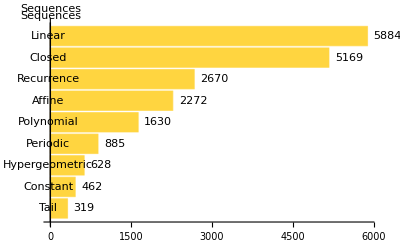

```mathematica
BarChart[Reverse[Lookup[p8["Methods"],"TestFits"]],BarOrigin->Left,ChartLabels->Reverse[Lookup[p8["Methods"],"Method"]],LabelingFunction->After,AxesLabel->{"Sequences",None}]
```

Figure 5. Sequences predicted from eight terms, by the method that found the program.

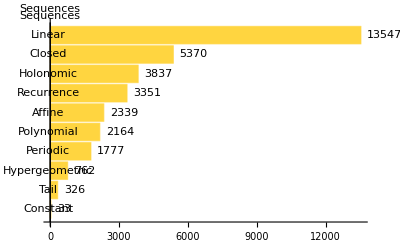

```mathematica
BarChart[Reverse[Lookup[p20["Methods"],"AllRecordedFits"]],BarOrigin->Left,ChartLabels->Reverse[Lookup[p20["Methods"],"Method"]],LabelingFunction->After,AxesLabel->{"Sequences",None}]
```

Figure 6. Sequences found from twenty terms that reproduce every later term, by method.

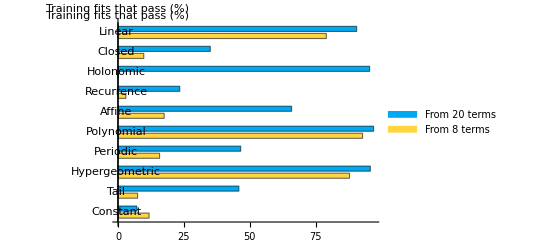

```mathematica
BarChart[Reverse[Transpose[{Lookup[passing[p8],Keys[passing[p20]],0],Values[passing[p20]]}]],BarOrigin->Left,ChartLabels->{Reverse[Keys[passing[p20]]],None},ChartLegends->{"From 8 terms","From 20 terms"},AxesLabel->{"Training fits that pass (%)",None}]
```

Figure 7. How often a program that fits its training terms also passes the held-out test. Solved constants hold; enumerated fits to eight terms often do not.

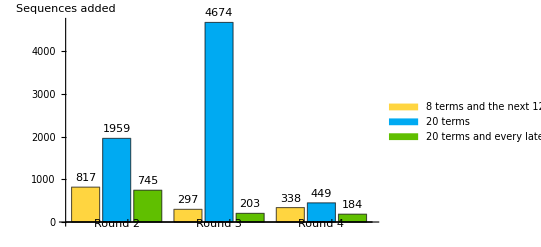

```mathematica
BarChart[Rest[Transpose[{Lookup[p8["Rounds"],"TestFits"],Lookup[p20["Rounds"],"TrainingFits"],Lookup[p20["Rounds"],"AllRecordedFits"]}]],ChartLabels->{Table["Round "<>ToString[round],{round,2,Length[p8["Rounds"]]}],None},ChartLegends->{"8 terms and the next 12","20 terms","20 terms and every later term"},LabelingFunction->Above,AxesLabel->{None,"Sequences added"}]
```

Figure 8. Sequences added after round 1, which finds 18,467, 53,117 and 32,374. Even rounds reuse subprograms found earlier as building blocks; odd rounds search deeper.

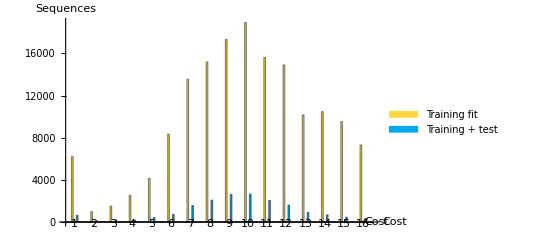

```mathematica
With[{costs=Select[p8["Costs"],#Cost≤16&]},BarChart[Lookup[costs,{"TrainingFits","TestFits"}],ChartLabels->{Lookup[costs,"Cost"],None},ChartLegends->{"Training fit","Training + test"},AxesLabel->{"Cost","Sequences"}]]
```

Figure 9. Program cost for fits to eight terms. Cheap programs keep predicting; costly fits rarely do.

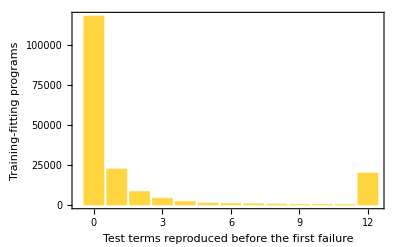

```mathematica
BarChart[p8["HeldOutAgreement"],ChartLabels->Range[0,12],Frame->True,FrameLabel->{"Test terms reproduced before the first failure","Training-fitting programs"}]
```

Figure 10. How many of the next twelve terms each eight-term fit reproduces. 19,919 programs reproduce all twelve.

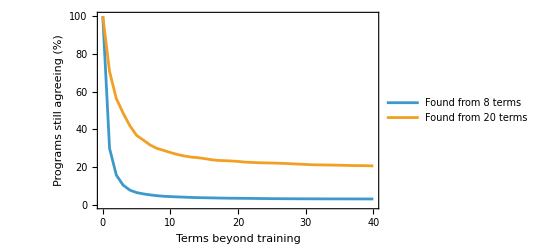

```mathematica
ListLinePlot[{(100. p8["Horizon"]["Agree"])/(p8["Horizon"]["Cohort"]),(100. p20["Horizon"]["Agree"])/(p20["Horizon"]["Cohort"])},DataRange->{0,40},PlotLegends->{"Found from 8 terms","Found from 20 terms"},Frame->True,FrameLabel->{"Terms beyond training","Programs still agreeing (%)"},PlotRange->{0,100}]
```

Figure 11. Programs whose sequences record at least forty later terms: the share that reproduces every term up to each distance.

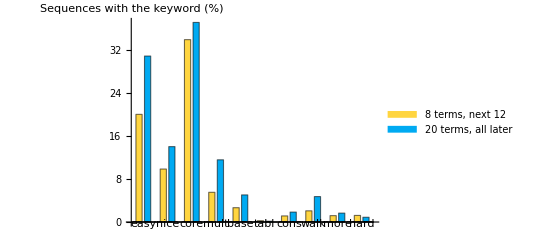

```mathematica
BarChart[Transpose[{(100. Lookup[p8["Keywords"],"TestFits"])/Lookup[p8["Keywords"],"Sequences"],(100. Lookup[p20["Keywords"],"TestFits"])/Lookup[p20["Keywords"],"Sequences"]}],ChartLabels->{Lookup[p8["Keywords"],"Keyword"],None},ChartLegends->{"8 terms, next 12","20 terms, all later"},AxesLabel->{None,"Sequences with the keyword (%)"}]
```

Figure 12. Share of each OEIS keyword's sequences that pass. Digit-based sequences (base), tables (tabl) and constants (cons) stay out of reach.

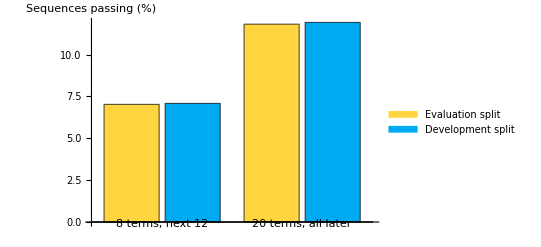

```mathematica
BarChart[{((100. #TestFits)/(#Sequences)&)/@Lookup[p8["Splits"],{"Evaluation","Development"}],((100. #AllRecordedFits)/(#Sequences)&)/@Lookup[p20["Splits"],{"Evaluation","Development"}]},ChartLabels->{{"8 terms, next 12","20 terms, all later"},None},ChartLegends->{"Evaluation split","Development split"},AxesLabel->{None,"Sequences passing (%)"}]
```

Figure 13. The development split, used for diagnostics while the method was built, and the untouched evaluation split agree.

## Programs that reproduce every recorded term

#### Prime numbers

```mathematica
program["A000040"]
```

Succ[Pred[Iter[Succ[Var],Const[0],Succ[WhileLoop[Acc,Let[Acc,Rem[Succ[Rec[Var,Const[1],Mul[Acc,Let[Succ[Idx],Var]]]],Succ[Var]]],Succ[Acc]]]]]]

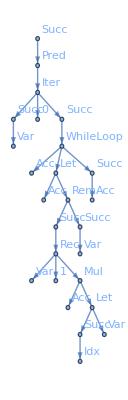

```mathematica
RecursorProgramTree[program["A000040"]]
```

Figure 14. Program found for A000040 from eight terms: the n-th m + 1 such that m + 1 divides m! + 1, which is Wilson's theorem.

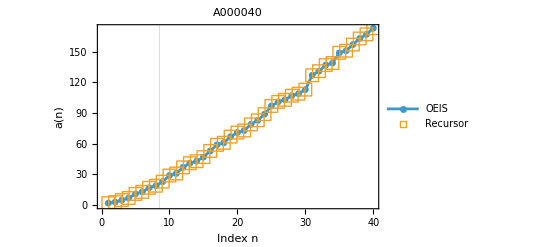

```mathematica
predictionPlot["A000040",40]
```

Figure 15. A000040: all 58 recorded terms are reproduced; the first 40 are shown. The vertical line ends the training terms.

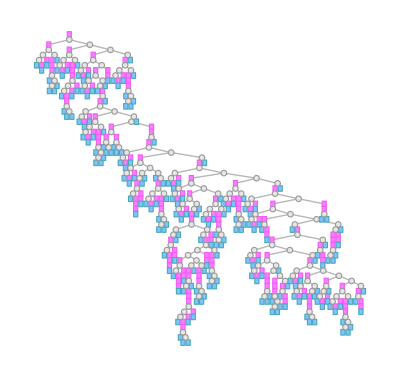

```mathematica
LambdaTree[CompileRecursor[program["A000040"]],PlotTheme->"Minimal"]
```

Figure 16. Compiled lambda tree for A000040.

#### Catalan numbers

```mathematica
program["A000108"]
```

Rec[Var,Const[1],Quot[Monus[Mul[Const[4],Mul[Succ[Idx],Acc]],Mul[Const[2],Acc]],Add[Const[1],Succ[Idx]]]]

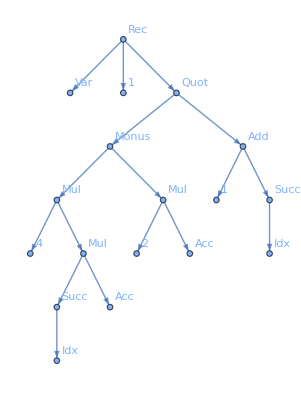

```mathematica
RecursorProgramTree[program["A000108"]]
```

Figure 17. Program found for A000108 from eight terms: a(n) = (4 n - 2) a(n-1)/(n + 1).

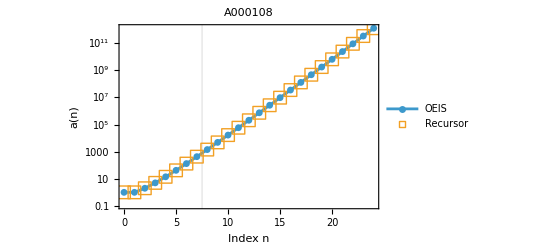

```mathematica
predictionPlot["A000108",25]
```

Figure 18. A000108: all 31 recorded terms are reproduced; the first 25 are shown. The vertical line ends the training terms.

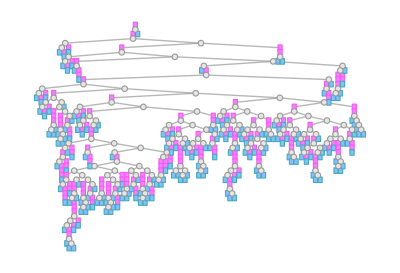

```mathematica
LambdaTree[CompileRecursor[program["A000108"]],PlotTheme->"Minimal"]
```

Figure 19. Compiled lambda tree for A000108.

#### Derangements

```mathematica
program["A000166"]
```

CoRec[Var,Ifz[Idx,Const[1],Ifz[Pred[Idx],Const[0],Mul[Pred[Idx],Add[CGet[Pred[Idx]],CGet[Pred[Pred[Idx]]]]]]]]

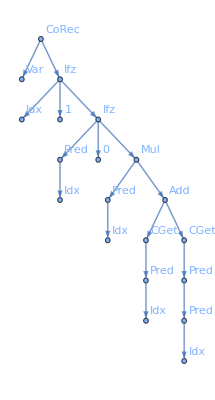

```mathematica
RecursorProgramTree[program["A000166"]]
```

Figure 20. Program found for A000166 from eight terms: a(n) = (n - 1) (a(n-1) + a(n-2)).

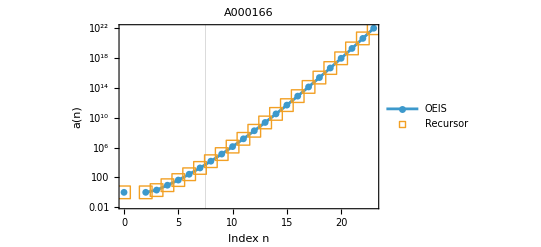

```mathematica
predictionPlot["A000166",24]
```

Figure 21. A000166: all 24 recorded terms are reproduced. The vertical line ends the training terms.

#### Binary weight

```mathematica
program["A000120"]
```

CoRec[Var,Ifz[Idx,Const[0],Add[CGet[Half[Idx]],Rem[Idx,Const[2]]]]]

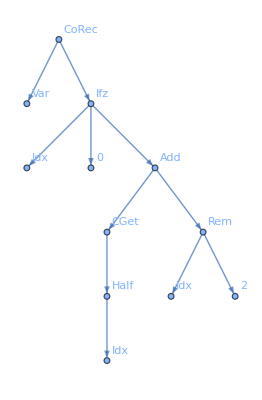

```mathematica
RecursorProgramTree[program["A000120"]]
```

Figure 22. Program found for A000120 from eight terms: a(n) = a(Quotient[n, 2]) + Mod[n, 2].

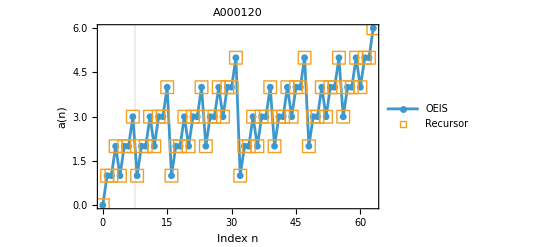

```mathematica
predictionPlot["A000120",64]
```

Figure 23. A000120: all 105 recorded terms are reproduced; the first 64 are shown. The vertical line ends the training terms.

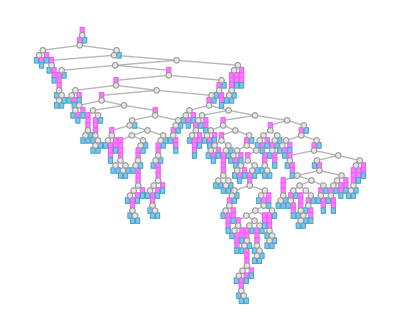

```mathematica
LambdaTree[CompileRecursor[program["A000120"]],PlotTheme->"Minimal"]
```

Figure 24. Compiled lambda tree for A000120.

#### Binary partitions

```mathematica
program["A000123"]
```

CoRec[Var,Ifz[Idx,Const[1],Add[CGet[Half[Idx]],CGet[Pred[Idx]]]]]

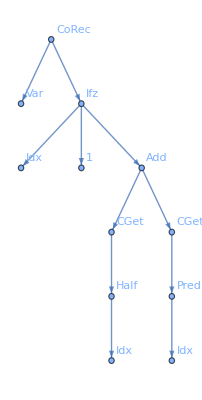

```mathematica
RecursorProgramTree[program["A000123"]]
```

Figure 25. Program found for A000123 from eight terms: a(n) = a(n-1) + a(Quotient[n, 2]).

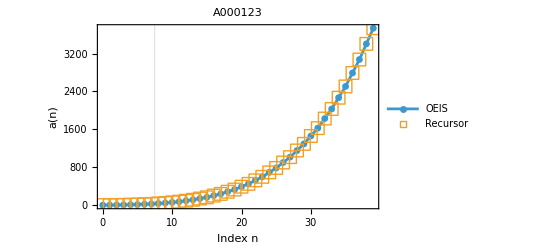

```mathematica
predictionPlot["A000123",40]
```

Figure 26. A000123: all 51 recorded terms are reproduced; the first 40 are shown. The vertical line ends the training terms.

#### Nonprime numbers

```mathematica
program["A018252"]
```

Pred[Iter[Var,Const[0],Succ[WhileLoop[Acc,Let[Acc,Rem[Rec[Var,Const[1],Mul[Acc,Let[Succ[Idx],Half[Succ[Var]]]]],Var]],Succ[Acc]]]]]

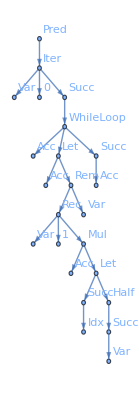

```mathematica
RecursorProgramTree[program["A018252"]]
```

Figure 27. Program found for A018252 from eight terms: the numbers m that divide the product of Ceiling[k/2] for k up to m.

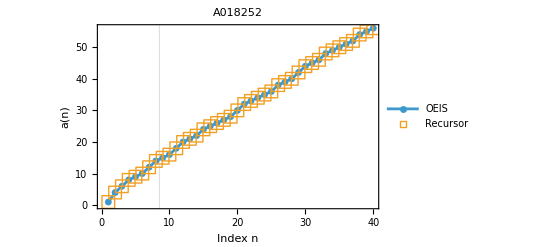

```mathematica
predictionPlot["A018252",40]
```

Figure 28. A018252: all 65 recorded terms are reproduced; the first 40 are shown. The vertical line ends the training terms.

#### Number of divisors

```mathematica
program["A000005"]
```

Monus[Let[Succ[Var],Rec[Var,Const[0],Add[Acc,Quot[Pred[Var],Idx]]]],Rec[Var,Const[0],Add[Acc,Quot[Pred[Var],Idx]]]]

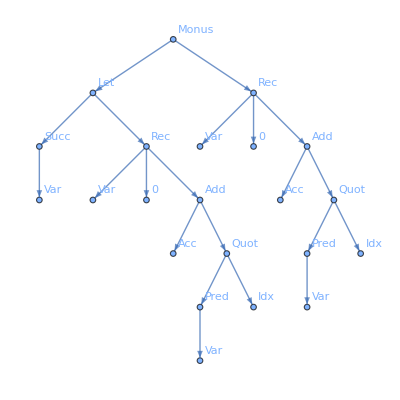

```mathematica
RecursorProgramTree[program["A000005"]]
```

Figure 29. Program found for A000005 from twenty terms: the difference of two sums of quotients, tau(n) = D(n) - D(n-1).

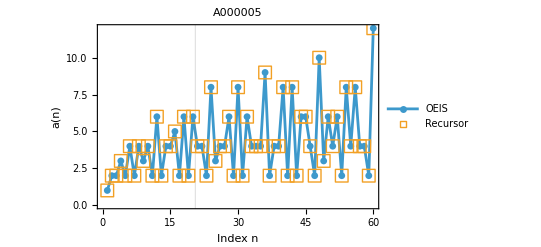

```mathematica
predictionPlot["A000005",60]
```

Figure 30. A000005: all 104 recorded terms are reproduced; the first 60 are shown. The vertical line ends the training terms.

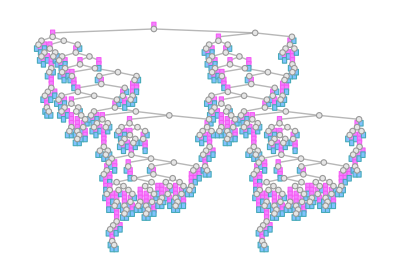

```mathematica
LambdaTree[CompileRecursor[program["A000005"]],PlotTheme->"Minimal"]
```

Figure 31. Compiled lambda tree for A000005.

#### Flavius Josephus's sieve

```mathematica
program["A000960"]
```

Succ[Rec[Var,Pred[Var],Add[Acc,Quot[Acc,Monus[Var,Idx]]]]]

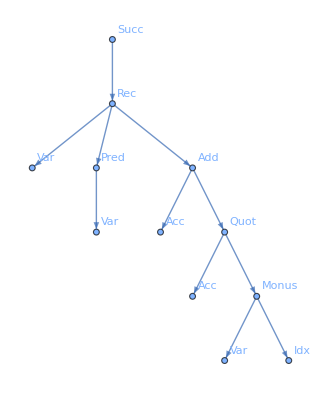

```mathematica
RecursorProgramTree[program["A000960"]]
```

Figure 32. Program found for A000960 from twenty terms: the index n - 1 is carried back through the sieving steps, j -> j + Quotient[j, d] for d = n, ..., 1.

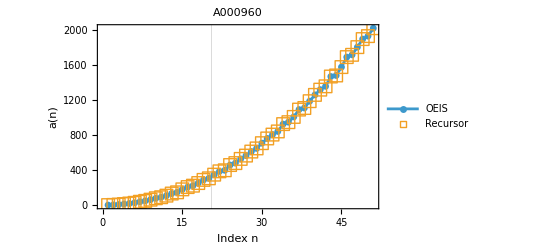

```mathematica
predictionPlot["A000960",51]
```

Figure 33. A000960: all 51 recorded terms are reproduced. The vertical line ends the training terms.

#### Motzkin numbers

```mathematica
program["A001006"]
```

CoRec[Var,Ifz[Idx,Const[1],Ifz[Pred[Idx],Const[1],Quot[Monus[Add[Add[CGet[Pred[Idx]],Mul[Const[2],Mul[Idx,CGet[Pred[Idx]]]]],Mul[Const[3],Mul[Idx,CGet[Pred[Pred[Idx]]]]]],Mul[Const[3],CGet[Pred[Pred[Idx]]]]],Add[Const[2],Idx]]]]]

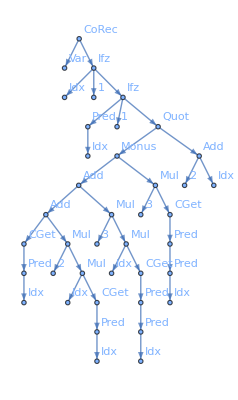

```mathematica
RecursorProgramTree[program["A001006"]]
```

Figure 34. Program found for A001006 from twenty terms: (n + 2) a(n) = (2 n + 1) a(n-1) + (3 n - 3) a(n-2).

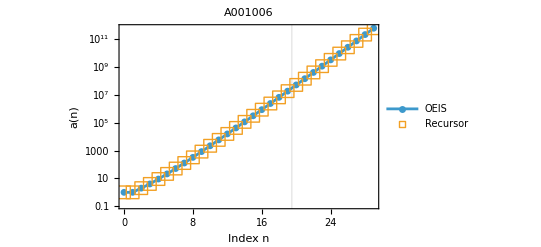

```mathematica
predictionPlot["A001006",30]
```

Figure 35. A001006: all 31 recorded terms are reproduced; the first 30 are shown. The vertical line ends the training terms.

#### Apéry numbers

```mathematica
program["A005258"]
```

CoRec[Var,Ifz[Idx,Const[1],Ifz[Pred[Idx],Const[3],Quot[Monus[Add[Add[Add[Mul[Const[3],CGet[Pred[Idx]]],Mul[Const[11],Mul[Mul[Idx,Idx],CGet[Pred[Idx]]]]],CGet[Pred[Pred[Idx]]]],Mul[Mul[Idx,Idx],CGet[Pred[Pred[Idx]]]]],Add[Mul[Const[11],Mul[Idx,CGet[Pred[Idx]]]],Mul[Const[2],Mul[Idx,CGet[Pred[Pred[Idx]]]]]]],Mul[Idx,Idx]]]]]

Found for A005258 from twenty terms: a three-term recurrence with quadratic coefficients.

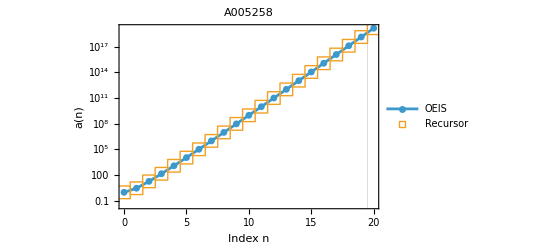

```mathematica
predictionPlot["A005258",21]
```

Figure 36. A005258: all 21 recorded terms are reproduced. The vertical line ends the training terms.

#### Baxter permutations

```mathematica
program["A001181"]
```

CoRec[Var,Ifz[Idx,Const[1],Ifz[Pred[Idx],Const[1],Quot[Monus[Add[Add[Add[Mul[Const[7],Mul[Idx,CGet[Pred[Idx]]]],Mul[Const[7],Mul[Mul[Idx,Idx],CGet[Pred[Idx]]]]],Mul[Const[16],CGet[Pred[Pred[Idx]]]]],Mul[Const[8],Mul[Mul[Idx,Idx],CGet[Pred[Pred[Idx]]]]]],Add[Mul[Const[2],CGet[Pred[Idx]]],Mul[Const[24],Mul[Idx,CGet[Pred[Pred[Idx]]]]]]],Add[Add[Const[6],Mul[Const[5],Idx]],Mul[Idx,Idx]]]]]]

Found for A001181 from twenty terms: a three-term recurrence with polynomial coefficients.

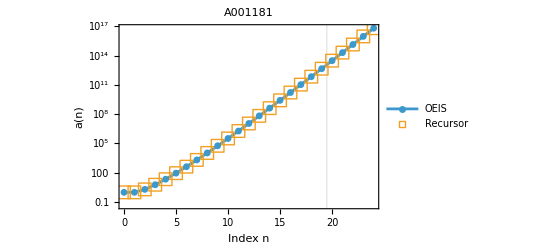

```mathematica
predictionPlot["A001181",25]
```

Figure 37. A001181: all 25 recorded terms are reproduced. The vertical line ends the training terms.

## Programs composed from learned building blocks

#### Sum of divisors

```mathematica
program["A000203"]
```

Let[Pred[Var],Monus[Let[Succ[Var],Rec[Var,Mul[Var,Var],Succ[Monus[Acc,Rem[Var,Idx]]]]],Rec[Var,Mul[Var,Var],Succ[Monus[Acc,Rem[Var,Idx]]]]]]

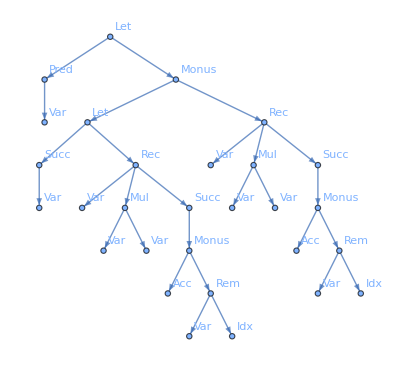

```mathematica
RecursorProgramTree[program["A000203"]]
```

Figure 38. Program found for A000203 from twenty terms: sigma(n) = S(n) - S(n-1), where S(m) is m^2 minus the remainders of m by the numbers below it.

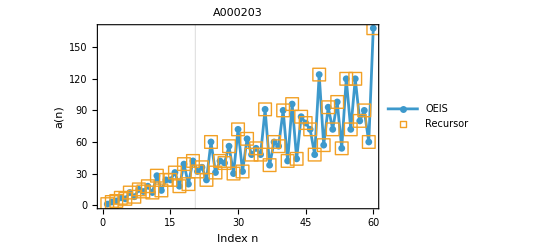

```mathematica
predictionPlot["A000203",60]
```

Figure 39. A000203: all 70 recorded terms are reproduced; the first 60 are shown. The vertical line ends the training terms.

#### Prime gaps

```mathematica
program["A001223"]
```

Monus[Let[Succ[Var],Pred[Iter[Succ[Var],Const[0],Succ[WhileLoop[Acc,Let[Let[Acc,Rec[Var,Var,Ifz[Rem[Var,Idx],Idx,Acc]]],Add[Monus[Var,Const[1]],Monus[Const[1],Var]]],Succ[Acc]]]]]],Pred[Iter[Succ[Var],Const[0],Succ[WhileLoop[Acc,Let[Let[Acc,Rec[Var,Var,Ifz[Rem[Var,Idx],Idx,Acc]]],Add[Monus[Var,Const[1]],Monus[Const[1],Var]]],Succ[Acc]]]]]]

Found for A001223 from twenty terms: the difference of two copies of a prime program that tests m by trial division.

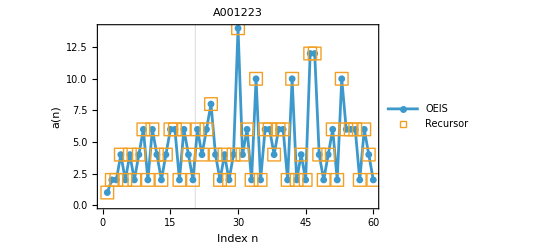

```mathematica
predictionPlot["A001223",60]
```

Figure 40. A001223: all 97 recorded terms are reproduced; the first 60 are shown. The vertical line ends the training terms.

#### Primorial numbers

```mathematica
program["A002110"]
```

Rec[Var,Const[1],Mul[Acc,Let[Succ[Idx],Succ[Pred[Iter[Succ[Var],Const[0],Succ[WhileLoop[Acc,Let[Acc,Rem[Succ[Rec[Var,Const[1],Mul[Acc,Let[Succ[Idx],Var]]]],Succ[Var]]],Succ[Acc]]]]]]]]]

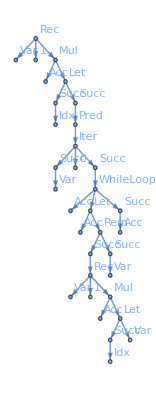

```mathematica
RecursorProgramTree[program["A002110"]]
```

Figure 41. Program found for A002110 from eight terms: the product of the first n primes, each from the Wilson program found in round 1.

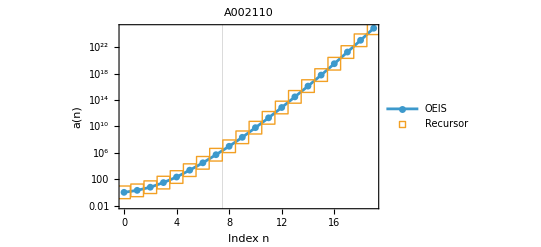

```mathematica
predictionPlot["A002110",20]
```

Figure 42. A002110: all 20 recorded terms are reproduced. The vertical line ends the training terms.

#### Fermat quotients

```mathematica
program["A007663"]
```

Half[Let[Succ[Pred[Iter[Succ[Var],Const[0],Succ[WhileLoop[Acc,Let[Acc,Rem[Succ[Rec[Var,Const[1],Mul[Acc,Let[Succ[Idx],Var]]]],Succ[Var]]],Succ[Acc]]]]]],Quot[Pred[Iter[Var,Const[1],Add[Acc,Acc]]],Var]]]

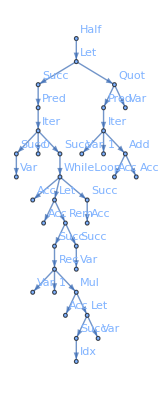

```mathematica
RecursorProgramTree[program["A007663"]]
```

Figure 43. Program found for A007663 from eight terms: half of Quotient[2^p - 1, p] at the n-th prime p.

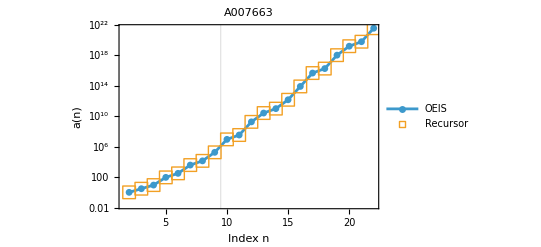

```mathematica
predictionPlot["A007663",21]
```

Figure 44. A007663: all 21 recorded terms are reproduced. The vertical line ends the training terms.

#### Paper-folding sequence

```mathematica
program["A014577"]
```

Rem[Succ[Half[Iter[Var,Var,Quot[Acc,Succ[Rem[Acc,Const[2]]]]]]],Const[2]]

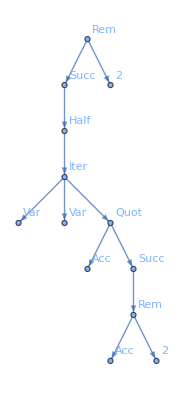

```mathematica
RecursorProgramTree[program["A014577"]]
```

Figure 45. Program found for A014577 from twenty terms: strip the trailing 1 bits of n, drop the next bit and return the complement of the bit after it.

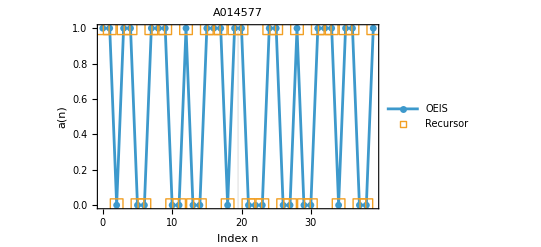

```mathematica
predictionPlot["A014577",40]
```

Figure 46. A014577: all 99 recorded terms are reproduced; the first 40 are shown. The vertical line ends the training terms.

#### Differences of Catalan numbers

```mathematica
program["A000245"]
```

Monus[Let[Succ[Var],Quot[Let[Add[Var,Var],Quot[Rec[Var,Const[1],Mul[Acc,Let[Succ[Idx],Var]]],Rec[Var,Const[1],Mul[Acc,Let[Succ[Idx],Half[Succ[Var]]]]]]],Succ[Var]]],Quot[Let[Add[Var,Var],Quot[Rec[Var,Const[1],Mul[Acc,Let[Succ[Idx],Var]]],Rec[Var,Const[1],Mul[Acc,Let[Succ[Idx],Half[Succ[Var]]]]]]],Succ[Var]]]

Found for A000245 from eight terms: Catalan(n + 1) - Catalan(n), with Catalan numbers built from two factorial programs.

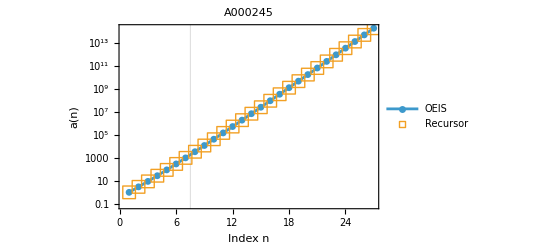

```mathematica
predictionPlot["A000245",28]
```

Figure 47. A000245: all 28 recorded terms are reproduced. The vertical line ends the training terms.

## Three programs for the primes

```mathematica
program["A000040-P20"]
```

Pred[Iter[Succ[Var],Const[0],Succ[WhileLoop[Acc,Let[Let[Acc,Iter[Var,Var,Succ[Rem[Add[Acc,Acc],Var]]]],Add[Monus[Var,Const[1]],Monus[Const[1],Var]]],Succ[Acc]]]]]

From twenty terms the search selects a different program for the primes than from eight.

```mathematica
test=First[Cases[program["A000040-P20"],Let[Acc,inner_]:>inner,∞]]
```

Iter[Var,Var,Succ[Rem[Add[Acc,Acc],Var]]]

```mathematica
accepted=Select[Range[2,700],EvaluateRecursor[test,#1]===1&];
```

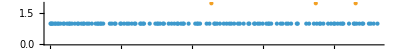

```mathematica
NumberLinePlot[{Select[accepted,PrimeQ],Select[accepted,!PrimeQ[#1]&]},PlotLegends->{"Prime","Composite"}]
```

Figure 48. Numbers below 700 that the test inside the twenty-term program accepts: every prime and three composites, 341, 561 and 645. The search found Fermat's test in base 2.

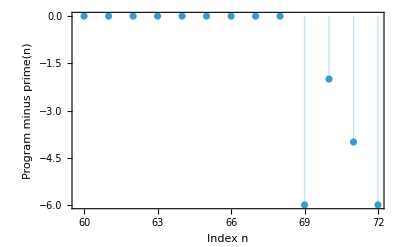

```mathematica
ListPlot[Table[EvaluateRecursor[program["A000040-P20"],n,"MaxSteps"->20000000,"TimeLimit"->60],{n,60,72}]-Prime[Range[60,72]],DataRange->{60,72},Filling->Axis,Frame->True,FrameLabel->{"Index n","Program minus prime(n)"}]
```

Figure 49. The twenty-term program gives the first 68 primes, ten more than the OEIS entry records, and then returns 341 = 11 × 31. Agreement on every recorded term is evidence, not proof.

```mathematica
Table[EvaluateRecursor[program["A000040"],n],{n,60,72}]===Prime[Range[60,72]]
```

False

The eight-term program rests on Wilson's theorem and stays exact.

```mathematica
trial=Last[program["A001223"]]
```

Pred[Iter[Succ[Var],Const[0],Succ[WhileLoop[Acc,Let[Let[Acc,Rec[Var,Var,Ifz[Rem[Var,Idx],Idx,Acc]]],Add[Monus[Var,Const[1]],Monus[Const[1],Var]]],Succ[Acc]]]]]

```mathematica
Table[EvaluateRecursor[trial,n],{n,60,72}]===Prime[Range[60,72]]
```

False

The prime gaps subtract two copies of a third program, which tests by trial division. It is exact too.

## Predictions that fail

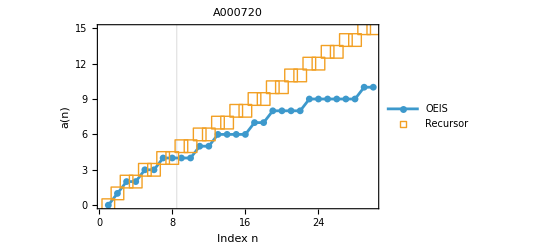

```mathematica
predictionPlot["A000720",30]
```

Figure 50. A000720: eight terms of the prime-counting function fit Mod[Quotient[n + 1, 2], n], which fails from the ninth term.

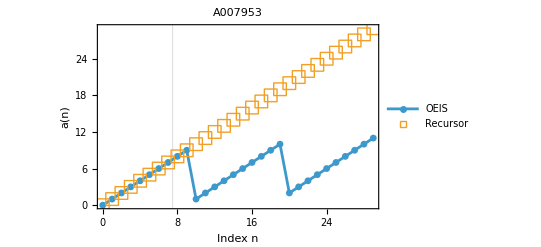

```mathematica
predictionPlot["A007953",30]
```

Figure 51. A007953: the digit sum of n is n itself for eight terms, and for ten.

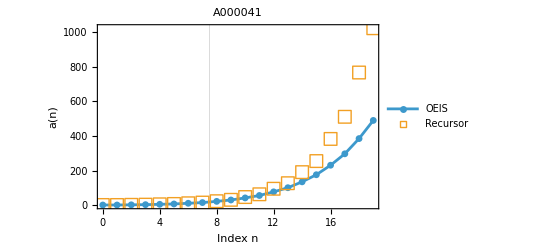

```mathematica
predictionPlot["A000041",20]
```

Figure 52. A000041: eight partition numbers fit a recurrence with three seeds; the ninth term differs.

## Search effort

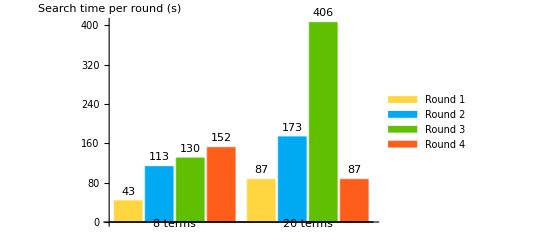

```mathematica
BarChart[{Lookup[p8["Rounds"],"SearchSeconds"],Lookup[p20["Rounds"],"SearchSeconds"]},ChartLabels->{{"8 terms","20 terms"},None},ChartLegends->Table["Round "<>ToString[round],{round,Length[p8["Rounds"]]}],LabelingFunction->(Placed[Round[#1],Above]&),AxesLabel->{None,"Search time per round (s)"}]
```

Figure 53. Search time of each round on twelve threads. One enumeration serves every sequence; corpus v1 ran 868,957 separate searches of 464 candidates.

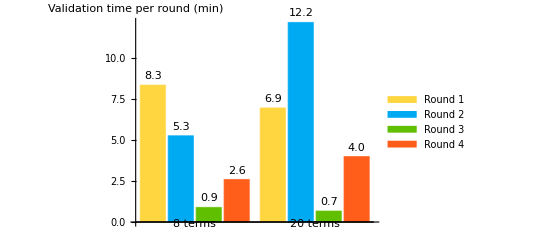

```mathematica
BarChart[{Lookup[p8["Rounds"],"ValidationSeconds"],Lookup[p20["Rounds"],"ValidationSeconds"]}/60.,ChartLabels->{{"8 terms","20 terms"},None},ChartLegends->Table["Round "<>ToString[round],{round,Length[p8["Rounds"]]}],LabelingFunction->(Placed[Slot["1"],Above]&),AxesLabel->{None,"Validation time per round (min)"}]
```

Figure 54. Time to check every proposed program with the reference interpreter on twelve kernels.